# Jenis2 EoS

```mathematica
Clear["Global`*"];
```

## Linear

```mathematica
EOSlin[p_]=3 p+240.;
```

## BST

```mathematica
FED1[P0_]=198.44659150368602+2.1700464559579813*P0+0.088730114353849*P0^2-0.00136997852494318*P0^3+0.000011358780185274*P0^4-5.97851057883043*10^(-8)*P0^5+2.1189092442107564*10^(-10)*P0^6-5.17833315779507*10^(-13)*P0^7+8.747685021941607*10^(-16)*P0^8-1.003326088565395*10^(-18)*P0^9+7.457832417744333*10^(-22)*P0^10-3.240190924875843*10^(-25)*P0^11+6.246104864722871*10^(-29)*P0^12;
FED2[P0_]=31.709610100869888+90.64073102501017*P0-29.153519698621*P0^2+5.4623392991109*P0^3-0.59924819745741*P0^4+0.041227991444036*P0^5-0.00186278195081703*P0^6+0.0000566704237195*P0^7-1.1680183124666673*10^(-6)*P0^8+1.6078512679724317*10^(-8)*P0^9-1.4153078467797958*10^(-10)*P0^10+7.20266639116908*10^(-13)*P0^11-1.6117637094790372*10^(-15)*P0^12;
FED3[P0_]=((P0-3.364*10^(-4))/(1.006*10^(-3)))^(3/4);
FED4[P0_]=7.405868060399274*10^(-4)+714.60658392886*P0-1.1556601395474602*10^(6)*P0^2+2.365618005585925*10^(9)*P0^3-1.752008202465829*10^(12)*P0^4;
EOSBST[p_]=Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]];
```

## G3 With Hyperon

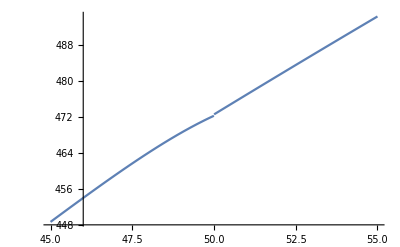
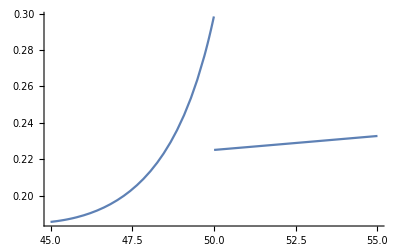

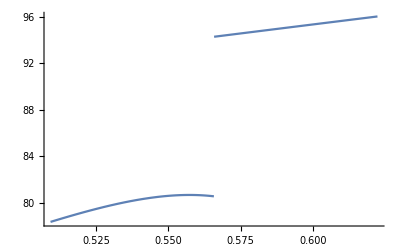
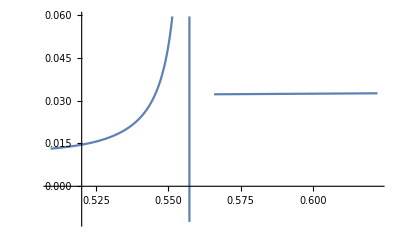

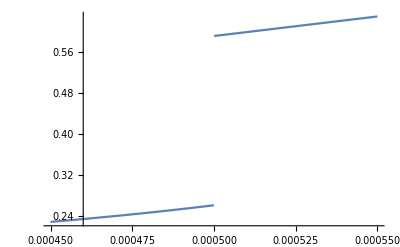
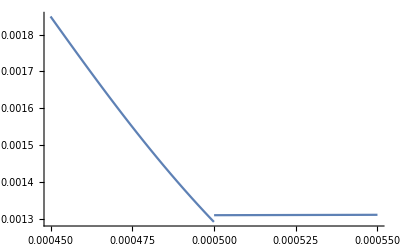

```mathematica
FED1[P0_]=207.22479761675402+6.279906372059321 P0-0.021350633175731673 P0^2+0.00003253273492751005 P0^3+1.4247301478353118*^-7 P0^4-5.796734043546596*^-10 P0^5+5.80259303998327*^-13 P0^6;
FED2[P0_]=75.7383014689123+34.578127397566746 P0-3.2678596692265187 P0^2+0.1855550164357522 P0^3-0.005427881210777648 P0^4+0.00007843713195849709 P0^5-4.444408879176666*^-7 P0^6;
FED3[P0_]=0.20731460615108688+769.3709388638298 P0-6186.523075294259 P0^2+31243.818621063823 P0^3-85543.05779411785 P0^4+117268.57170356606 P0^5-62995.352300066246 P0^6;
FED4[P0_]=0.00020663104786834376+985.755096204799 P0-6.452649548410587*^6 P0^2+4.045493650683301*^10 P0^3-1.2422017897553961*^14 P0^4+1.7654930953548538*^17 P0^5-9.152941701213566*^19 P0^6;
EOSWH[p_]=Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]];

{Plot[EOSWH[p],{p,50.*0.9,50.*1.1}],Plot[1/EOSWH'[p],{p,50.*0.9,50.*1.1}]}
{Plot[EOSWH[p],{p,0.5658*0.9,0.5658*1.1}],Plot[1/EOSWH'[p],{p,0.5658*0.9,0.5658*1.1}]}
{Plot[EOSWH[p],{p,5.*10^(-4)*0.9,5.*10^(-4)*1.1}],Plot[1/EOSWH'[p],{p,5.*10^(-4)*0.9,5.*10^(-4)*1.1}]}
```

## G3 With Hyperon and Speed of Sound Restricted at high density

```mathematica
FED1[P0_]=56.336121316129855+11.816705939891484 P0-0.08998007668063691 P0^2+0.0004060689424004221 P0^3-9.838173200421972*^-7 P0^4+1.219639435236914*^-9 P0^5-6.069131445225517*^-13 P0^6;
FED2[P0_]=39.041069188205+56.501467482692085 P0-6.899733785115867 P0^2+0.43992222641441237 P0^3-0.01402554956168195 P0^4+0.000217264619919116 P0^5-1.3035407417179315*^-6 P0^6;
FED3[P0_]=0.20731460615108688+769.3709388638298 P0-6186.523075294259 P0^2+31243.818621063823 P0^3-85543.05779411785 P0^4+117268.57170356606 P0^5-62995.352300066246 P0^6;
FED4[P0_]=0.00020663104786834376+985.755096204799 P0-6.452649548410587*^6 P0^2+4.045493650683301*^10 P0^3-1.2422017897553961*^14 P0^4+1.7654930953548538*^17 P0^5-9.152941701213566*^19 P0^6;
EOSWHSS[p_]=Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]];
```

## G3 Without Hyperon

```mathematica
FED1[P0_]=234.1942349585189+4.244398207462238 P0-0.013395621016951648 P0^2+0.000045526410778733156 P0^3-8.910615387698381*^-8 P0^4+9.208285152708568*^-11 P0^5-3.8734411956242993*^-14 P0^6;
FED2[P0_]=77.11157896904827+33.27601430502912 P0-3.000040277276358 P0^2+0.1672231023157756 P0^3-0.004965419482658063 P0^4+0.00007352155777361597 P0^5-4.266615225505047*^-7 P0^6;
FED3[P0_]=0.20731460615108688+769.3709388638298 P0-6186.523075294259 P0^2+31243.818621063823 P0^3-85543.05779411785 P0^4+117268.57170356606 P0^5-62995.352300066246 P0^6;
FED4[P0_]=0.00020663104786834376+985.755096204799 P0-6.452649548410587*^6 P0^2+4.045493650683301*^10 P0^3-1.2422017897553961*^14 P0^4+1.7654930953548538*^17 P0^5-9.152941701213566*^19 P0^6;
EOSWoutH[p_]=Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]];
```

## G3 Without Hyperon but Speed of Sound Restricted at high density

```mathematica
FED1[P0_]=293.11268673102506+3.10114370497162 P0-0.010901925280260074 P0^2+0.00004154068779880557 P0^3-8.163579780831742*^-8 P0^4+7.974755635410319*^-11 P0^5-3.063161763646646*^-14 P0^6;
FED2[P0_]=77.11157896904827+33.27601430502912 P0-3.000040277276358 P0^2+0.1672231023157756 P0^3-0.004965419482658063 P0^4+0.00007352155777361597 P0^5-4.266615225505047*^-7 P0^6;
FED3[P0_]=0.20731460615108688+769.3709388638298 P0-6186.523075294259 P0^2+31243.818621063823 P0^3-85543.05779411785 P0^4+117268.57170356606 P0^5-62995.352300066246 P0^6;
FED4[P0_]=0.00020663104786834376+985.755096204799 P0-6.452649548410587*^6 P0^2+4.045493650683301*^10 P0^3-1.2422017897553961*^14 P0^4+1.7654930953548538*^17 P0^5-9.152941701213566*^19 P0^6;
EOSWoutHSS[p_]=Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]];
```

## Quark Star

```mathematica
EOSQS[p_]=(197.282+3.50745 p-0.000267588 p^2+8.79024*10^-8 p^3-1.38896*10^-11 p^4+8.28846*10^-16 p^5);
```

## Cara fitting baru

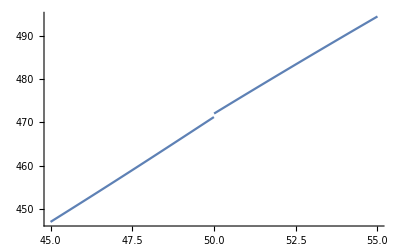
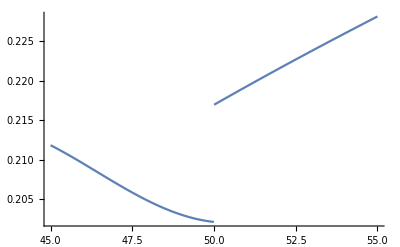

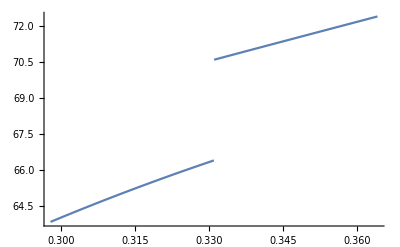
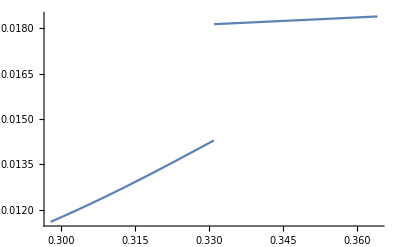

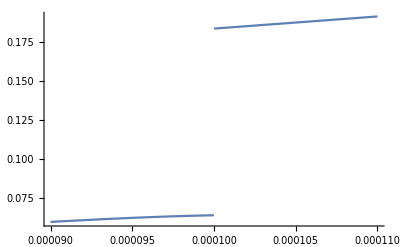
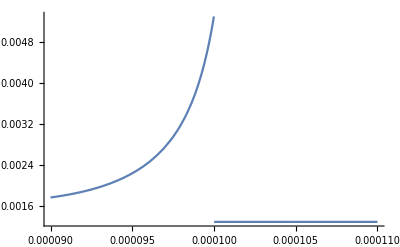

```mathematica
FED1[P0_]:=-5.06792720791983*^-25 P0^12+1.2667992545501144*^-21 P0^11-1.4024689980426383*^-18 P0^10+9.062047900662808*^-16 P0^9-3.792648318013163*^-13 P0^8+1.0794063234335766*^-10 P0^7-2.136137992101247*^-8 P0^6+2.9578978853768754*^-6 P0^5-0.0002849065702296197 P0^4+0.01877875987337337 P0^3-0.828664235905911 P0^2+26.978499551010707 P0-33.628585452726405
FED2[P0_]:=-6.999113545123572*^-17 P0^12+3.865531430452677*^-14 P0^11-9.390700300258363*^-12 P0^10+1.319800212815305*^-9 P0^9-1.1875300820352649*^-7 P0^8+7.152135765179124*^-6 P0^7-0.00029302719682713755 P0^6+0.008147475301127988 P0^5-0.15107819237682044 P0^4+1.8096086901180817 P0^3-13.359668774030693 P0^2+63.42156851177051 P0+51.01562276111647
FED3[P0_]:=-66485.29459441072 P0^6+123214.68602275256 P0^5-89355.30945979558 P0^4+32380.61124525787 P0^3-6343.1367063658445 P0^2+777.7743141742344 P0+0.10561351223961706
FED4[P0_]:=-7.933215404530278*^23 P0^6+2.4261603696434594*^20 P0^5-2.853861252866049*^16 P0^4+1.6321510739067363*^12 P0^3-4.8567157045778826*^7 P0^2+1383.024036075485 P0+0.0000765259444829395
(*
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]];
*)
EOSWHnew[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.33097<p≤50.},{FED3[p],1.*10^(-4)<p≤0.33097}},FED4[p]]; 

{Plot[EOSWHnew[p],{p,50.*0.9,50.*1.1}],Plot[1/EOSWHnew'[p],{p,50.*0.9,50.*1.1}]}
{Plot[EOSWHnew[p],{p,0.33097*0.9,0.33097*1.1}],Plot[1/EOSWHnew'[p],{p,0.33097*0.9,0.33097*1.1}]}
{Plot[EOSWHnew[p],{p,1.*10^(-4)*0.9,1.*10^(-4)*1.1}],Plot[1/EOSWHnew'[p],{p,1.*10^(-4)*0.9,1.*10^(-4)*1.1}]}
```

## Tes kalau semua data langsung fitting saja

```mathematica
EOScrudeWH[P0_]:=35.38875313226208+17.24847480749493 P0-0.2448168236745378 P0^2+0.0020467888116389543 P0^3-8.782852352403798*^-6 P0^4+1.8483442745836703*^-8 P0^5-1.5101080861937848*^-11 P0^6
```

## Pilih EoS

```mathematica
ClearAll[EOS]
EOS[p_]:=EOSlin[p];
```

# Hitung satu profil

```mathematica
(* Konstanta -----------------------------------------------------*)
l=IntegerPart[2]; 
Λ=-3*10.^-9;
κ=38.*^6; 
λ=Λ κ+1; 
G=1.323790281083862 10^-12;
c=299792458.;
ms=1.1154605324408694 10^15;
rs=1000.;

(* Persamaan Love Number ------------------------------------------*)
a12[cb_]=0; b12[cb_]=15/8 1/cb^3;
a22[cb_]=1/3 cb^2; b22[cb_]=0; 
a32[cb_]=113/84 cb^2; b32[cb_]=1787/392 1/cb^3;
a42[cb_]=13/9 cb^2; b42[cb_]=-(3305/448+(5 π^2)/7+(15 Log[2]^2)/7) 1/cb^3;

a13[cb_]=0; b13[cb_]=35/8 1/cb^4;
a23[cb_]=1/45 cb^3; b23[cb_]=0; 
a33[cb_]=127/756 cb^3; b33[cb_]=24805/1512 1/cb^4;
a43[cb_]=158/945 cb^3; b43[cb_]=-(13795/576+(25 π^2)/9+(25 Log[2]^2)/3) 1/cb^4;

a14[cb_]=0; b14[cb_]=735/64 1/cb^5;
a24[cb_]=1/630 cb^4; b24[cb_]=0; 
a34[cb_]=7613/465696 cb^4; b34[cb_]=469685/5808 1/cb^5;
a44[cb_]=200077/10866240 cb^4; b44[cb_]=-(14680085/202752+(875 π^2)/88+(2625 Log[2]^2)/88) 1/cb^5;

f12[x_]=1+(21 x)/4-(46 x^2)/7-(59 x^3)/4-x^4/7+6 x^5+(8 x^6)/7;
f22[x_]=3/56  (113 Log[x-1]+15 Log[1+x]);
f32[x_]=235/56+(1357 x)/56-(1469 x^2)/84-(1987 x^3)/84+(2057 x^4)/168+(389 x^5)/56-(8 x^6)/7;
f42[x_]=-25/14+(153 x)/14+(171 x^2)/14-(17 x^3)/14-(25 x^4)/7-(4 x^5)/7;
f52[x_]=-25/14+(34 x)/7-(93 x^2)/14+(13 x^3)/7+(4 x^4)/7;
f62[x_]=-24/7  (Log[x-1] Log[(1+x)/4]+2 PolyLog[2,(1-x)/2]);

f13[x_]=20 x+(185 x^2)/4-(220 x^3)/7-(375 x^4)/4-(20 x^5)/7+40 x^6+(20 x^7)/3;
f23[x_]=25/56 x (127 Log[x-1]+Log[1+x]);
f33[x_]=-32+(8941 x)/168+(7305 x^2)/56-(9977 x^3)/84-(35845 x^4)/252+(5225 x^5)/72+(8195 x^6)/168-(20 x^7)/3;
f43[x_]=-635/21-(845 x)/42+(195 x^2)/2+(3425 x^3)/42-(925 x^4)/42-(70 x^5)/3-(10 x^6)/3;
f53[x_]=5/21+(135 x)/14+(20 x^2)/7-(1315 x^3)/42+(40 x^4)/3+(10 x^5)/3;
f63[x_]=-200/7 x(Log[x-1] Log[(1+x)/4]+2 PolyLog[2,(1-x)/2]);

f14[x_]=-615/64-(1225 x)/32+(342515 x^2)/4928+(14405 x^3)/48-(202325 x^4)/4928-(14305 x^5)/32-(277315 x^6)/4928+175 x^7+(595 x^8)/22;
f24[x_]=(25 (-1+7 x^2) (7613 Log[-1+x]+67 Log[1+x]))/4928;
f34[x_]=-2160637/44352-(7430627 x)/44352+(169207 x^2)/448+(7841513 x^3)/14784-(3123931 x^4)/4928-(8024815 x^5)/14784+(14823115 x^6)/44352+(1159715 x^7)/6336-(595 x^8)/22;
f44[x_]=-3735/308-(6715 x)/28-(42865 x^2)/308+(154025 x^3)/308+(113875 x^4)/308-(38235 x^5)/308-(4445 x^6)/44-(595 x^7)/44;
f54[x_]=-3735/308+(535 x)/77+(30455 x^2)/308-(4540 x^3)/77-(34285 x^4)/308+(665 x^5)/11+(595 x^6)/44;
f64[x_]=-1500/77 (-1+7 x^2) (Log[-1+x] Log[(1+x)/4]+2 PolyLog[2,(1-x)/2]);

Q2[cb_]=Evaluate[FunctionExpand[LegendreQ[2,2,3,x]]/.x->1/cb-1];
Q3[cb_]=Evaluate[FunctionExpand[LegendreQ[3,2,3,x]]/.x->1/cb-1];
Q4[cb_]=Evaluate[FunctionExpand[LegendreQ[4,2,3,x]]/.x->1/cb-1];
P2[cb_]=Evaluate[LegendreP[2,2,3,x]/.x->1/cb-1];
P3[cb_]=Evaluate[LegendreP[3,2,3,x]/.x->1/cb-1];
P4[cb_]=Evaluate[LegendreP[4,2,3,x]/.x->1/cb-1];
T2[cb_]=Evaluate[f32[x]/((x+1)(x-1)^2)+f42[x]/(x+1)Log[x-1]+f52[x]((x+1)/(x-1))Log[x+1]+(x^2-1)f62[x]/.x-> 1/cb-1];
T3[cb_]=Evaluate[f33[x]/((x+1)(x-1)^2)+f43[x]/(x+1)Log[x-1]+f53[x]((x+1)/(x-1))Log[x+1]+(x^2-1)f63[x]/.x-> 1/cb-1];
T4[cb_]=Evaluate[f34[x]/((x+1)(x-1)^2)+f44[x]/(x+1)Log[x-1]+f54[x]((x+1)/(x-1))Log[x+1]+(x^2-1)f64[x]/.x-> 1/cb-1];
S2[cb_]=Evaluate[f12[x]/(x^2-1)+(x^2-1)f22[x]/.x->1/cb-1];
S3[cb_]=Evaluate[f13[x]/(x^2-1)+(x^2-1)f23[x]/.x->1/cb-1];
S4[cb_]=Evaluate[f14[x]/(x^2-1)+(x^2-1)f24[x]/.x->1/cb-1];

Qb2[cb_,yb_]=yb Q2[cb]+cb D[Q2[cb],cb];
Pb2[cb_,yb_]=yb P2[cb]+cb D[P2[cb],cb];
Tb2[cb_,yb_]=yb T2[cb]+cb D[T2[cb],cb];
Sb2[cb_,yb_]=yb S2[cb]+cb D[S2[cb],cb];

Qb3[cb_,yb_]=yb Q3[cb]+cb D[Q3[cb],cb];
Pb3[cb_,yb_]=yb P3[cb]+cb D[P3[cb],cb];
Tb3[cb_,yb_]=yb T3[cb]+cb D[T3[cb],cb];
Sb3[cb_,yb_]=yb S3[cb]+cb D[S3[cb],cb];

Qb4[cb_,yb_]=yb Q4[cb]+cb D[Q4[cb],cb];
Pb4[cb_,yb_]=yb P4[cb]+cb D[P4[cb],cb];
Tb4[cb_,yb_]=yb T4[cb]+cb D[T4[cb],cb];
Sb4[cb_,yb_]=yb S4[cb]+cb D[S4[cb],cb];

kb2[cb_,ϵb_,yb_]=-((2 2-1)!!)/2((a12[cb]+ϵb a32[cb])Qb2[cb,yb]+(a22[cb]+ϵb a42[cb])Pb2[cb,yb]+ϵb(a12[cb]Tb2[cb,yb]+a22[cb]Sb2[cb,yb]))((b12[cb]+ϵb b32[cb])Qb2[cb,yb]+(b22[cb]+ϵb b42[cb])Pb2[cb,yb]+ϵb(b12[cb]Tb2[cb,yb]+b22[cb]Sb2[cb,yb]))^-1; 
kb3[cb_,ϵb_,yb_]=-((2 3-1)!!)/2((a13[cb]+ϵb a33[cb])Qb3[cb,yb]+(a23[cb]+ϵb a43[cb])Pb3[cb,yb]+ϵb(a13[cb]Tb3[cb,yb]+a23[cb]Sb3[cb,yb]))((b13[cb]+ϵb b33[cb])Qb3[cb,yb]+(b23[cb]+ϵb b43[cb])Pb3[cb,yb]+ϵb(b13[cb]Tb3[cb,yb]+b23[cb]Sb3[cb,yb]))^-1; 
kb4[cb_,ϵb_,yb_]=-((2 4-1)!!)/2((a14[cb]+ϵb a34[cb])Qb4[cb,yb]+(a24[cb]+ϵb a44[cb])Pb4[cb,yb]+ϵb(a14[cb]Tb4[cb,yb]+a24[cb]Sb4[cb,yb]))((b14[cb]+ϵb b34[cb])Qb4[cb,yb]+(b24[cb]+ϵb b44[cb])Pb4[cb,yb]+ϵb(b14[cb]Tb4[cb,yb]+b24[cb]Sb4[cb,yb]))^-1; 

(* Persamaan Keadaan --------------------------------------------*)
ρ[p_]=EOS[p];
a[r_]=√Abs[λ+8π G κ ρ[p[r]]];
b[r_]=√Abs[λ-8π G κ p[r]];
cs[r_]=√(1/D[ρ[p[r]],p[r]]);

(* Persamaan Differensial ----------------------------------------*)
eq1[r_]=If[κ== 0,-p'[r]-G/r^2(p[r]+ρ[p[r]])(4π r^3 p[r]+m[r]-(r^3 Λ)/(3 G))(1-(2m[r] G)/r-(Λ r^2)/3)^-1,-p'[r]-1/(4π G κ)(1/(2κ)(1/(a[r]b[r])+a[r]/b[r]^3-2)r+(2m[r]G)/r^2+(Λ r)/(3λ))(4/(a[r]^2-b[r]^2)+3/b[r]^2+1/(a[r]^2 cs[r]^2))^-1(1-(2m[r]G)/r-(Λ r^2)/(3λ))^-1];
eq2[r_]=If[κ==0,-m'[r]+4π r^2 ρ[p[r]],-m'[r]+r^2/(4 G κ)(2/λ-3/(a[r]b[r])+a[r]/b[r]^3)];
eq3[r_]=-β'[r]-2p'[r](2π G κ(3/b[r]^2+1/(a[r]^2 cs[r]^2))+1/(ρ[p[r]]+p[r]));

α[r_]=-Log[1-(2m[r]G)/r-(Λ r^2)/(3λ)];
f[r_]=If[κ==0,1/r+ⅇ^α[r](1/r+4π G(p[r]-ρ[p[r]])r),1/r+ⅇ^α[r]/r+ⅇ^α[r]/κ(1/(a[r]b[r])-1)r];
g[r_]=If[κ==0,-(l(l+1)ⅇ^α[r])/r^2+4π G ⅇ^α[r](5ρ[p[r]]+9p[r]+(ρ[p[r]]+p[r])/cs[r]^2)-β'[r]^2,-((l(l+1)ⅇ^α[r])/r^2+(2 ⅇ^α[r])/κ+β'[r]^2)+2 ⅇ^α[r]/κ a[r]/b[r]^3(2-(4/(a[r]^2-b[r]^2))(4/(a[r]^2-b[r]^2)+3/b[r]^2+1/(a[r]^2 cs[r]^2))^-1)];
eq4[r_]=-y'[r]+y[r]/r-y[r]^2/r-y[r]f[r]-r g[r];

(* Nilai batas r,p,m,β,y --------------------------------------*)
r0=10^-9;rn=10.^12;
m0=0.;
p0=300.;
β0=1.;
y0=l;

(* Logaritma integrasi untuk menghitung rb,mb --------------------*)
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
clearStatus[]:=showStatus[""];
clearStatus[]
Do[
Clear[mbs,rbs];
sol=First[NDSolve[{eq1[r]==0,eq2[r]==0,eq3[r]==0,eq4[r]==0,m[r0]==m0 , p[r0]==p0,β[r0]==β0,y[r0]== y0,WhenEvent[p[r]<1.*^-8,{rbs=r,"StopIntegration"}]},{p,m,β,y},{r,r0,rn},Method->{"EquationSimplification"->"Residual"},EvaluationMonitor:>showStatus["p,r = "<>ToString[CForm[p[r]]]<>","<>ToString[CForm[r]]]]];
mbs=Re[Evaluate[m[rbs]/.sol]];
β0=(Log[1-(2mbs G)/rbs-(Λ rbs^2)/(3λ)]-Evaluate[β[rbs]/.sol])+β0;
,{j,1,2}]; 

(* Plot Profil *)
(*Plot[Evaluate[p[r]/. sol],{r,r0,rbs},PlotRange->All,PlotLabel->p[r]]
Plot[Evaluate[m[r]/. sol],{r,r0,rbs},PlotRange->All,PlotLabel->m[r]]
Plot[Evaluate[β[r]/. sol],{r,r0,rbs},PlotRange->All,PlotLabel->β[r]]
Plot[Evaluate[y[r]/. sol],{r,r0,rbs},PlotRange->All,PlotLabel->y[r]]*)

cbs=(mbs G)/rbs;
ϵbs=(Λ mbs^2 G^2)/λ;
ybs=Evaluate[y[rbs]/.sol];
kbs2=kb2[cbs,ϵbs,ybs];
kbs3=kb3[cbs,ϵbs,ybs];
kbs4=kb4[cbs,ϵbs,ybs];

po[r_]:=Evaluate[p[r]/. sol]
mo[r_]:=Evaluate[m[r]/. sol]

If[l==2,N[{l,p0,rbs/1000,mo[rbs]/ms,ybs,kbs2}],]
If[l==3,N[{l,p0,rbs/1000,mo[rbs]/ms,ybs,kbs3}],]
If[l==4,N[{l,p0,rbs/1000,mo[rbs]/ms,ybs,kbs4}],]
```

```mathematica
{2.,300.,11.216827406672712,2.23623014204561,1.8289995381617048,0.013793902289605434}
{3.,300.,11.21682739574728,2.2362301774572684,3.8241838438486275,0.002788611197998081}
{4.,300.,11.216827530441817,2.236230236486032,5.583059785984171,0.0007267624105401383}
```

```mathematica
Series[((a12+eps a32)Qb2+(a22+eps a42)Pb2+eps(a12 Tb2+a22 Sb2))((b12+eps b32)Qb2+(b22+eps b42)Pb2+eps(b12 Tb2+b22 Sb2))^-1,{eps,0,1}]//Simplify//Normal//FortranForm
```

(a22*Pb2 + a12*Qb2)/(b22*Pb2 + b12*Qb2) + 
     -  (eps*((b22*Pb2 + b12*Qb2)*
     -        (a42*Pb2 + a32*Qb2 + a22*Sb2 + a12*Tb2) - 
     -       (a22*Pb2 + a12*Qb2)*
     -        (b42*Pb2 + b32*Qb2 + b22*Sb2 + b12*Tb2)))/
     -   (b22*Pb2 + b12*Qb2)**2

```mathematica
Series[((a13+eps a33)Qb3+(a23+eps a43)Pb3+eps(a13 Tb3+a23 Sb3))((b13+eps b33)Qb3+(b23+eps b43)Pb3+eps(b13 Tb3+b23 Sb3))^-1,{eps,0,1}]//Simplify//Normal//FortranForm
```

(a23*Pb3 + a13*Qb3)/(b23*Pb3 + b13*Qb3) + 
     -  (eps*((b23*Pb3 + b13*Qb3)*
     -        (a43*Pb3 + a33*Qb3 + a23*Sb3 + a13*Tb3) - 
     -       (a23*Pb3 + a13*Qb3)*
     -        (b43*Pb3 + b33*Qb3 + b23*Sb3 + b13*Tb3)))/
     -   (b23*Pb3 + b13*Qb3)**2

```mathematica
Series[((a14+eps a34)Qb4+(a24+eps a44)Pb4+eps(a14 Tb4+a24 Sb4))((b14+eps b34)Qb4+(b24+eps b44)Pb4+eps(b14 Tb4+b24 Sb4))^-1,{eps,0,1}]//Simplify//Normal//FortranForm
```

(a24*Pb4 + a14*Qb4)/(b24*Pb4 + b14*Qb4) + 
     -  (eps*((b24*Pb4 + b14*Qb4)*
     -        (a44*Pb4 + a34*Qb4 + a24*Sb4 + a14*Tb4) - 
     -       (a24*Pb4 + a14*Qb4)*
     -        (b44*Pb4 + b34*Qb4 + b24*Sb4 + b14*Tb4)))/
     -   (b24*Pb4 + b14*Qb4)**2

# Bikin fungsi PolyLog(2,(1/C-1))

```mathematica
str[number_,precision_]:=ToString[FortranForm[SetPrecision[number,precision]]];

(* Konstanta ---------------------------------------------------*)
l=IntegerPart[2]; 
Λ=-3*10.^-9;
κ=38.`*^+6; 
λ=Λ κ+1; 
G=1.323790281083862 10^-12;
c=299792458.;
ms=1.1154605324408694 10^15;
rs=1000.;

(* Persamaan Love Number -----------------------------------------*)
Subscript[a1, 2][cb_]=0; Subscript[b1, 2][cb_]=15/8 1/cb^3;
Subscript[a2, 2][cb_]=1/3 cb^2; Subscript[b2, 2][cb_]=0; 
Subscript[a3, 2][cb_]=113/84 cb^2; Subscript[b3, 2][cb_]=1787/392 1/cb^3;
Subscript[a4, 2][cb_]=13/9 cb^2; Subscript[b4, 2][cb_]=-(3305/448+(5 π^2)/7+(15 Log[2]^2)/7) 1/cb^3;

Subscript[a1, 3][cb_]=0; Subscript[b1, 3][cb_]=35/8 1/cb^4;
Subscript[a2, 3][cb_]=1/45 cb^3; Subscript[b2, 3][cb_]=0; 
Subscript[a3, 3][cb_]=127/756 cb^3; Subscript[b3, 3][cb_]=24805/1512 1/cb^4;
Subscript[a4, 3][cb_]=158/945 cb^3; Subscript[b4, 3][cb_]=-(13795/576+(25 π^2)/9+(25 Log[2]^2)/3) 1/cb^4;

Subscript[a1, 4][cb_]=0; Subscript[b1, 4][cb_]=735/64 1/cb^5;
Subscript[a2, 4][cb_]=1/630 cb^4; Subscript[b2, 4][cb_]=0; 
Subscript[a3, 4][cb_]=7613/465696 cb^4; Subscript[b3, 4][cb_]=469685/5808 1/cb^5;
Subscript[a4, 4][cb_]=200077/10866240 cb^4; Subscript[b4, 4][cb_]=-(14680085/202752+(875 π^2)/88+(2625 Log[2]^2)/88) 1/cb^5;

Subscript[f1, 2][x_]=1+(21 x)/4-(46 x^2)/7-(59 x^3)/4-x^4/7+6 x^5+(8 x^6)/7;
Subscript[f2, 2][x_]=3/56  (113 Log[x-1]+15 Log[1+x]);
Subscript[f3, 2][x_]=235/56+(1357 x)/56-(1469 x^2)/84-(1987 x^3)/84+(2057 x^4)/168+(389 x^5)/56-(8 x^6)/7;
Subscript[f4, 2][x_]=-25/14+(153 x)/14+(171 x^2)/14-(17 x^3)/14-(25 x^4)/7-(4 x^5)/7;
Subscript[f5, 2][x_]=-25/14+(34 x)/7-(93 x^2)/14+(13 x^3)/7+(4 x^4)/7;
Subscript[f6, 2][x_]=-24/7  (Log[x-1] Log[(1+x)/4]+2 PolyLog[2,(1-x)/2]);

Subscript[f1, 3][x_]=20 x+(185 x^2)/4-(220 x^3)/7-(375 x^4)/4-(20 x^5)/7+40 x^6+(20 x^7)/3;
Subscript[f2, 3][x_]=25/56 x (127 Log[x-1]+Log[1+x]);
Subscript[f3, 3][x_]=-32+(8941 x)/168+(7305 x^2)/56-(9977 x^3)/84-(35845 x^4)/252+(5225 x^5)/72+(8195 x^6)/168-(20 x^7)/3;
Subscript[f4, 3][x_]=-635/21-(845 x)/42+(195 x^2)/2+(3425 x^3)/42-(925 x^4)/42-(70 x^5)/3-(10 x^6)/3;
Subscript[f5, 3][x_]=5/21+(135 x)/14+(20 x^2)/7-(1315 x^3)/42+(40 x^4)/3+(10 x^5)/3;
Subscript[f6, 3][x_]=-200/7 x(Log[x-1] Log[(1+x)/4]+2 PolyLog[2,(1-x)/2]);

Subscript[f1, 4][x_]=-615/64-(1225 x)/32+(342515 x^2)/4928+(14405 x^3)/48-(202325 x^4)/4928-(14305 x^5)/32-(277315 x^6)/4928+175 x^7+(595 x^8)/22;
Subscript[f2, 4][x_]=(25 (-1+7 x^2) (7613 Log[-1+x]+67 Log[1+x]))/4928;
Subscript[f3, 4][x_]=-2160637/44352-(7430627 x)/44352+(169207 x^2)/448+(7841513 x^3)/14784-(3123931 x^4)/4928-(8024815 x^5)/14784+(14823115 x^6)/44352+(1159715 x^7)/6336-(595 x^8)/22;
Subscript[f4, 4][x_]=-3735/308-(6715 x)/28-(42865 x^2)/308+(154025 x^3)/308+(113875 x^4)/308-(38235 x^5)/308-(4445 x^6)/44-(595 x^7)/44;
Subscript[f5, 4][x_]=-3735/308+(535 x)/77+(30455 x^2)/308-(4540 x^3)/77-(34285 x^4)/308+(665 x^5)/11+(595 x^6)/44;
Subscript[f6, 4][x_]=-1500/77 (-1+7 x^2) (Log[-1+x] Log[(1+x)/4]+2 PolyLog[2,(1-x)/2]);

Subscript[Q, l][cb_]=Evaluate[FunctionExpand[LegendreQ[l,2,3,x]]/.x->1/cb-1];
Subscript[P, l][cb_]=Evaluate[LegendreP[l,2,3,x]/.x->1/cb-1];
Subscript[T, l][cb_]=Evaluate[(Subscript[f3, l][x])/((x+1)(x-1)^2)+(Subscript[f4, l][x])/(x+1)Log[x-1]+Subscript[f5, l][x]((x+1)/(x-1))Log[x+1]+(x^2-1)Subscript[f6, l][x]/.x-> 1/cb-1];
Subscript[S, l][cb_]=Evaluate[(Subscript[f1, l][x])/(x^2-1)+(x^2-1)Subscript[f2, l][x]/.x->1/cb-1];

Subscript[Qb, l][cb_,yb_]=yb Subscript[Q, l][cb]+cb D[Subscript[Q, l][cb],cb];
Subscript[Pb, l][cb_,yb_]=yb Subscript[P, l][cb]+cb D[Subscript[P, l][cb],cb];
Subscript[Tb, l][cb_,yb_]=yb Subscript[T, l][cb]+cb D[Subscript[T, l][cb],cb];
Subscript[Sb, l][cb_,yb_]=yb Subscript[S, l][cb]+cb D[Subscript[S, l][cb],cb];

kb[cb_,ϵb_,yb_]=-((2l-1)!!)/2((Subscript[a1, l][cb]+ϵb Subscript[a3, l][cb])Subscript[Qb, l][cb,yb]+(Subscript[a2, l][cb]+ϵb Subscript[a4, l][cb])Subscript[Pb, l][cb,yb]+ϵb(Subscript[a1, l][cb]Subscript[Tb, l][cb,yb]+Subscript[a2, l][cb]Subscript[Sb, l][cb,yb]))((Subscript[b1, l][cb]+ϵb Subscript[b3, l][cb])Subscript[Qb, l][cb,yb]+(Subscript[b2, l][cb]+ϵb Subscript[b4, l][cb])Subscript[Pb, l][cb,yb]+ϵb(Subscript[b1, l][cb]Subscript[Tb, l][cb,yb]+Subscript[b2, l][cb]Subscript[Sb, l][cb,yb]))^-1; 

(* Buka file ------------------------------------------------*)
filename=OpenWrite[FileNameJoin[{NotebookDirectory[],StringTemplate["tidal(l=``,k=``,L=``).dat"][l,str[κ,3],str[Λ,3]]}],FormatType->OutputForm];

(* Persamaan Keadaan --------------------------------------------*)
ρ[p_]=EOS[p];
a[r_]=√Abs[λ+8π G κ ρ[p[r]]];
b[r_]=√Abs[λ-8π G κ p[r]];
cs[r_]=√(1/D[ρ[p[r]],p[r]]);

(* Persamaan Differensial ----------------------------------------*)
eq1[r_]=If[κ== 0,-p'[r]-G/r^2(p[r]+ρ[p[r]])(4π r^3 p[r]+m[r]-(r^3 Λ)/(3 G))(1-(2m[r] G)/r-(Λ r^2)/3)^-1,-p'[r]-1/(4π G κ)(1/(2κ)(1/(a[r]b[r])+a[r]/b[r]^3-2)r+(2m[r]G)/r^2+(Λ r)/(3λ))(4/(a[r]^2-b[r]^2)+3/b[r]^2+1/(a[r]^2 cs[r]^2))^-1(1-(2m[r]G)/r-(Λ r^2)/(3λ))^-1];
eq2[r_]=If[κ==0,-m'[r]+4π r^2 ρ[p[r]],-m'[r]+r^2/(4 G κ)(2/λ-3/(a[r]b[r])+a[r]/b[r]^3)];
eq3[r_]=-β'[r]-2p'[r](2π G κ(3/b[r]^2+1/(a[r]^2 cs[r]^2))+1/(ρ[p[r]]+p[r]));

α[r_]=-Log[1-(2m[r]G)/r-(Λ r^2)/(3λ)];
f[r_]=If[κ==0,1/r+ⅇ^α[r](1/r+4π G(p[r]-ρ[p[r]])r),1/r+ⅇ^α[r]/r+ⅇ^α[r]/κ(1/(a[r]b[r])-1)r];
g[r_]=If[κ==0,-(l(l+1)ⅇ^α[r])/r^2+4π G ⅇ^α[r](5ρ[p[r]]+9p[r]+(ρ[p[r]]+p[r])/cs[r]^2)-β'[r]^2,-((l(l+1)ⅇ^α[r])/r^2+(2 ⅇ^α[r])/κ+β'[r]^2)+2 ⅇ^α[r]/κ a[r]/b[r]^3(2-(4/(a[r]^2-b[r]^2))(4/(a[r]^2-b[r]^2)+3/b[r]^2+1/(a[r]^2 cs[r]^2))^-1)];
eq4[r_]=-y'[r]+y[r]/r-y[r]^2/r-y[r]f[r]-r g[r];

(* Jalankan p0 -----------------------------------------------*)
pa=1.;pb=600.;n=0;i=100;
While[n≤i,{

(* Nilai batas r,p,m,β,y ------------------------------------*)
r0=10^-9;rn=10.^12;
p0=Exp[Log[pa]+n (Log[pb]-Log[pa])/i];
m0=0.;
β0=1.;
y0=l;

(* Logaritma integrasi untuk menghitung rb,mb ------------------*)
Do[
Clear[mbs,rbs];
sol=First[NDSolve[{eq1[r]==0,eq2[r]==0,eq3[r]==0,eq4[r]==0,m[r0]==m0 , p[r0]==p0,β[r0]==β0,y[r0]== y0,WhenEvent[p[r]==0,{rbs=r,"StopIntegration"}]},{p,m,β,y},{r,r0,rn},Method->{"EquationSimplification"->"Residual"}]];

mbs=Re[Evaluate[m[rbs]/.sol]];
β0=(Log[1-(2mbs G)/rbs-(Λ rbs^2)/(3λ)]-Evaluate[β[rbs]/.sol])+β0;
,{j,1,2}]; 

(* Hitung cb,yb,kb -----------------------------------------*)
cbs=(mbs G)/rbs;
ϵbs=(Λ mbs^2 G^2)/λ;
ybs=Evaluate[y[rbs]/.sol];
kbs=kb[cbs,ϵbs,ybs];

(* Tulis data ----------------------------------------------*)
Write[filename,str[rbs/rs,17]," ",str[mbs/ms,17]," ",str[cbs,17]," ",str[kbs,17]," ",str[(2 kbs)/(3 cbs^5),17]," "];

Print[n];

n++}];

(* Tutup File *)
Close[filename];

(* Atur ulang isi file output *)
ffname=FileNameJoin[{NotebookDirectory[],StringTemplate["tidal(l=``,k=``,L=``).dat"][l,str[κ,3],str[Λ,3]]}];
ff=OpenRead[ffname];
dataff=ReadList[ff,{Number,Number,Number,Number,Number}];
Close[ff];
Export[ffname,dataff]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

C:\Users\ilham\Dropbox\00 momin tidal G3eos EiBI\00 tidal EiBI\0-Numerik-tidal\nb\tidal(l=2,k=3.8e7,L=-3.e-9).dat

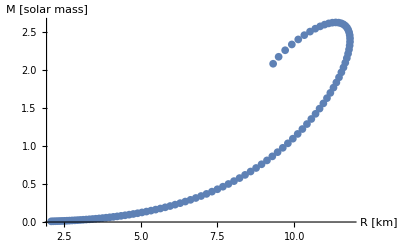

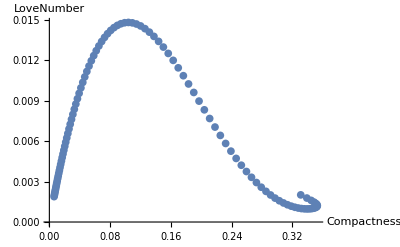

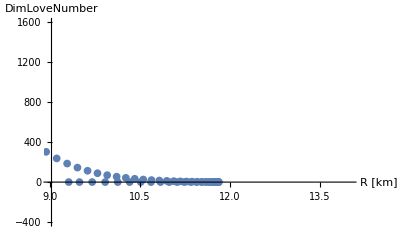

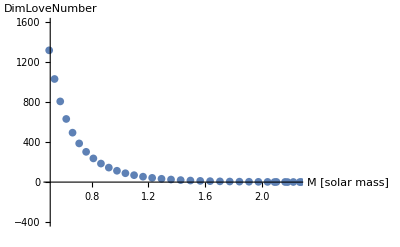

```mathematica
str[number_,precision_]:=ToString[FortranForm[SetPrecision[number,precision]]];
l=IntegerPart[2]; 
Λ=-3*10.^-9;
κ=38*10.^6; 
data=Import[FileNameJoin[{NotebookDirectory[],StringTemplate["tidal(l=``,k=``,L=``).dat"][l,str[κ,3],str[Λ,3]]}]];
ListPlot[data[[All,{1,2}]],AxesLabel->{"R [km]","M [solar mass]"}]
ListPlot[data[[All,{3,4}]],AxesLabel->{"Compactness","LoveNumber"}]
ListPlot[data[[All,{1,5}]],AxesLabel->{"R [km]","DimLoveNumber"},PlotRange->{{9,14},{-400,1600}}]
ListPlot[data[[All,{2,5}]],AxesLabel->{"M [solar mass]","DimLoveNumber"},PlotRange->{{0.5,2.25},{-400,1600}}]
```

#### COBA FITTING POLYLOGNYA SBG FUNGSI COMPACTNESS

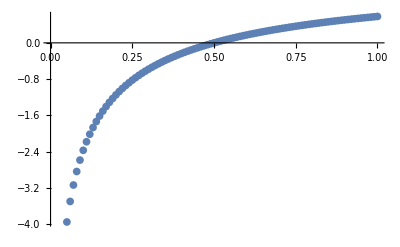

-4.90013+0.000169323/x^2-0.066073/x+67.8137 x-661.371 x^2+4714.74 x^3-23715.7 x^4+84334.4 x^5-213247. x^6+383602. x^7-486337. x^8+424031. x^9-241719. x^10+81048.4 x^11-12113.3 x^12

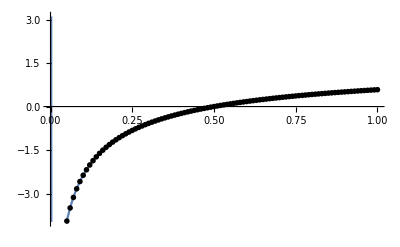

-4.900128181312306 + 0.00016932349271285354/x**2 - 
     -  0.06607300001104759/x + 67.81366827244638*x - 
     -  661.3708294454829*x**2 + 4714.740202946316*x**3 - 
     -  23715.678000133867*x**4 + 84334.3662190509*x**5 - 
     -  213246.7648131581*x**6 + 383601.9350809346*x**7 - 
     -  486336.6093429251*x**8 + 424030.9280758699*x**9 - 
     -  241718.87649564294*x**10 + 81048.35624350267*x**11 - 
     -  12113.292172158068*x**12

```mathematica
datangasal=Table[{0.01*n,PolyLog[2,(1-(1/(0.01*n)-1))/2]},{n,1,100}];
ListPlot[datangasal]
fitted=Fit[datangasal,{x^-2,x^-1,1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12},x]
Plot[fitted,{x,0.0001,1},Epilog->{PointSize[0.01],Map[Point,datangasal]}]
fitted//FortranForm
```

```mathematica
(* 100 data *)
-4.900128181312306+0.00016932349271285354/x**2--0.06607300001104759/x+67.81366827244638*x--661.3708294454829*x**2+4714.740202946316*x**3--23715.678000133867*x**4+84334.3662190509*x**5--213246.7648131581*x**6+383601.9350809346*x**7--486336.6093429251*x**8+424030.9280758699*x**9--241718.87649564294*x**10+81048.35624350267*x**11--12113.292172158068*x**12
```

```mathematica
(* 1000 data *)
-8.809174251010777 + 0.000010784110982139273/x**2 - 
     -  0.023067915835877233/x + 217.25079886156087*x - 
     -  3511.687215002784*x**2 + 35548.81591950086*x**3 - 
     -  229940.60401625358*x**4 + 986039.7487548694*x**5 - 
     -  2.879746796273323e6*x**6 + 5.806277264496892e6*x**7 - 
     -  8.07460560163354e6*x**8 + 7.599912317973219e6*x**9 - 
     -  4.620440319672904e6*x**10 + 1.6368130814606736e6*x**11 - 
     -  256554.09126465503*x**12
```

```mathematica
LegendreP[4,2,3,XX]//FunctionExpand//FortranForm
```

(15*(1 - XX)**2*(1 + XX)*(-1 + 7*XX**2))/(2.*(-1 + XX))

#### DIBETULIN LAGI POLYLOGNYA SALAH TERNYATA DI 0 sd 0.01

```mathematica
Evaluate[FunctionExpand[LegendreQ[2,2,3,x]]]
Evaluate[FunctionExpand[LegendreQ[3,2,3,x]]]
Evaluate[FunctionExpand[LegendreQ[4,2,3,x]]]
Evaluate[LegendreP[2,2,3,x]]
Evaluate[LegendreP[3,2,3,x]]
Evaluate[LegendreP[4,2,3,x]]
```

6 (-1+x) (1+x) (-(-1+x)^2/(48 (1+x)^2)+(-1+x)/(6 (1+x))-(1+x)/(6 (-1+x))+(1+x)^2/(48 (-1+x)^2)+1/4 (-Log[-1+x]+Log[1+x]))

45 (-1+x) (1+x)^2 (-(-1+x)^3/(720 (1+x)^3)+(-1+x)^2/(48 (1+x)^2)-(1+x)/(48 (-1+x))+(1+x)^2/(720 (-1+x)^2)+1/12 (-4/3-Log[-1+x]+Log[1+x])+((-1+x) (4/3-Log[-1+x]+Log[1+x]))/(12 (1+x)))

540 (-1+x) (1+x)^3 (-(-1+x)^4/(17280 (1+x)^4)+(-1+x)^3/(720 (1+x)^3)-(1+x)/(720 (-1+x))+(1+x)^2/(17280 (-1+x)^2)+1/96 (-25/12-Log[-1+x]+Log[1+x])+((-1+x) (-Log[-1+x]+Log[1+x]))/(36 (1+x))+((-1+x)^2 (25/12-Log[-1+x]+Log[1+x]))/(96 (1+x)^2))

(3 (1-x)^2 (1+x))/(-1+x)

(15 (1-x)^2 x (1+x))/(-1+x)

(15 (1-x)^2 (1+x) (-1+7 x^2))/(2 (-1+x))

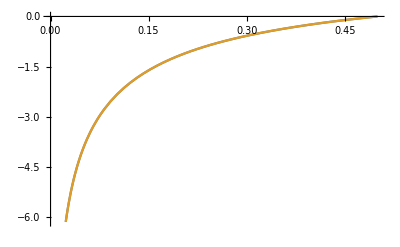

```mathematica
PLG[x_]:=Piecewise[{{-4.900128181312306+0.00016932349271285354/(x^2)-0.06607300001104759/x+67.81366827244638*x -661.3708294454829*x^2+4714.740202946316*x^3-23715.678000133867*x^4+84334.3662190509*x^5-213246.7648131581*x^6+383601.9350809346*x^7-486336.6093429251*x^8+424030.9280758699*x^9-241718.87649564294*x^10+81048.35624350267*x^11-12113.292172158068*x^12,0.01<x≤0.5},{5827.173801180173-5875.9257455803145/x^(1/1000)+67,0.<x≤0.01}},x]
Plot[{PLG[cb],PolyLog[2,(1-(1/cb-1))/2]},{cb,0,1/2},PlotRange->{{0.0,0.5},Automatic}]
```

```mathematica
5827.173801180173-5875.9257455803145/x^(1/1000)+67//FortranForm
```

5894.173801180173 - 
     -  5875.9257455803145/
     -   x**0.001

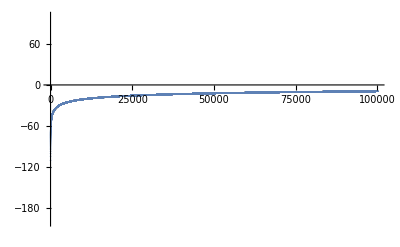

```mathematica
ListPlot[Table[PolyLog[2,(1-(1/(0.01*x/100000)-1))/2],{x,1,100000}],PlotRange->{-200,100}]
```

```mathematica
fungsi[x_]=Fit[Table[PolyLog[2,(1-(1/(0.01*x/1000)-1))/2],{x,1,1000}],{1/x^(1/1000),1(*,Log[x]^3*)(*,x^2,x^3,x^4,x^5,x^6,x^7,x^8*)},x]
```

5827.17-5875.93/x^(1/1000)

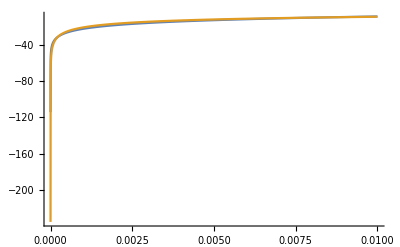

```mathematica
Plot[{fungsi[cb]+67(*+26*),PolyLog[2,(1-(1/cb-1))/2]},{cb,0,0.01},PlotRange->All]
```

```mathematica
Simplify[(1-(1/cb-1))/2]
```

1-1/(2 cb)

```mathematica
TraditionalForm[PolyLog[2,(1-x)/2]]
```

2(1-x)/2

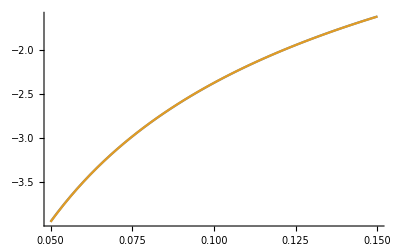

```mathematica
Plot[{PolyLog[2,(1-(1/cb-1))/2],PLG[cb]},{cb,0.05,0.15},PlotRange->All]
```